## Branching processes

In a branching process, individuals die and reproduce independently of each other.   Thus, the outcome from multiple individuals can be reduced to the outcome from a single individual. Individuals may change type, leading to a multi-type branching process.

#### Simulating discrete-time birth death

i) 
The transition matrix for a branching process has a special form, in which the i'th row depends only on the first row, M_(1,j). In our example we have 3 possible states 0, 1 and 2. I define the first row of a matrix M as:
M1,0 - the probability of 1 individual having 0 offspring
M1,1 - the probability that 1 individual stays in the same state
M1,2 - the probability that 1 individual has two offspring.

Given the birth-death probabilities the first row of M follows:
M1,0 = d
M1,1 = 1-b-d
M1,2 = b

Since μ=∑_(j=0)^∞ j M_(1,j) μ = 0*d + 1*(1-b-d) + 2b = 1 -d + b. 
Now, if μ < 1, because -d + b =0 has to satisfy b < d. In other words, if μ < 1 the value of birth rate has to be lower that the death rate. The probability of of one individual (F0) leaving offspring in the first F1 generation is calculated as P_1=1- Q_1 where Q_1=∑_(j=0)^∞ M_(1,j)Q_1^j 
and for t generations in the future
Q_((t),1)=∑_(j=0)^∞ M_(1,j)Q_((t-1),1)^j=(M̃)_1[Q_((t-1),1)]
If we assume Poisson distribution of offspring number, (M̃)_1[z]=ⅇ^(-λ(1-z)) the probability of one individual leaving offspring in the distant future we therefore in our case depend on the value of μ =1 - d + b.

Some examples with calculations: If we assign values to b and d such that 1 - d + b > 1 we can apply Poisson generation function and calculate the probability of an individual leaving 0 offspring at time t. In this example b=0.2, d=0.1, and t =20 (as distant generation in future). Because 1 - d + b > 1 the probability is 0.197637.

```mathematica
poissonGF[b_, d_][z_]:=Exp[-(1-d+b)(1-z)];
1- Flatten[{1/(0!)D[Nest[poissonGF[0.2, 0.1],z,20],{z,0}]/.z->0}]
```

{0.197637}

If we however set values of b and d such that 1 - d + b < 1, so b < d, (b =0.1, d=0.2the probability in t=20 is 0.0236689 instead.

```mathematica
poissonGF[b_, d_][z_]:=Exp[-(1-d+b)(1-z)];
1- Flatten[{1/(0!)D[Nest[poissonGF[0.1, 0.2],z,20],{z,0}]/.z->0}]
```

{0.0236689}

ii) 

The expected number of members in generation n(t) is equal to n(t)=μ^t, where µ is the expected number of offspring for each individual μ=∑_(j=0)^∞ j M_(1,j). Therefore, if μ<1, the expectation tends to zero, implying that extinction is inevitable.  However, if μ>1, the expectation increases exponentially, implying that there is at least some probability of survival. If however μ=1 the extinction is also inevitable.  We can see that the E[Xn] converges to 0, 1 or ∞ depending on whether  μ is < 1, = 1, or > 1.

Simulations. All simulations start with 1 individual.
First I simulate μ is < 1. As I showed above in this case, b < d must be satisfied. In all replicates E[Xn] converges to 0.

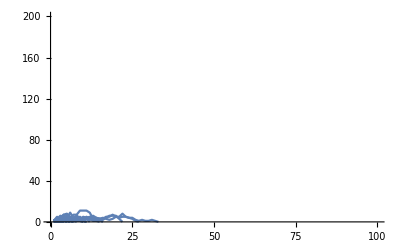

```mathematica
newN[b_, d_, gen_][i_]:=If[i==0,0,RandomInteger[PoissonDistribution[(1-d+b)i]]];
mulow=Table[NestWhileList[newN[0.1, 0.2, 10],1,Positive,1,100],{100}];
Show[Table[ListLinePlot[mulow⟦i⟧,PlotRange->{{0,100},{0,200}}],{i,100}]]
```

Then, I simulate μ is = 1. As Here, b = d. This mean that each individual is replaced by 1 in each generation. The process is of extinction is inevitable, but some replicates can persist for a long time and in example plot below.

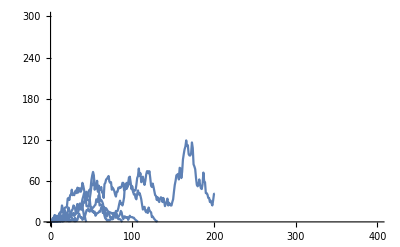

```mathematica
newN[b_, d_, gen_][i_]:=If[i==0,0,RandomInteger[PoissonDistribution[(1-d+b)i]]];
muone=Table[NestWhileList[newN[0.1, 0.1, 10],1,Positive,1,200],{100}];
Show[Table[ListLinePlot[muone⟦i⟧,PlotRange->{{0,400},{0,300}}],{i,100}]]
```

Then, I simulate μ is > 1. As Here, b > d is necessary.  E[Xn] converges to  ∞ in some replicates, although still some replicates die out.

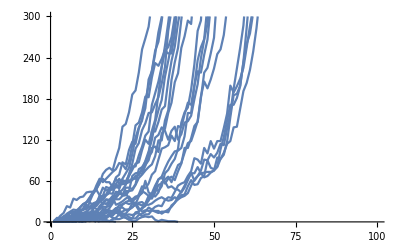

```mathematica
newN[b_, d_, gen_][i_]:=If[i==0,0,RandomInteger[PoissonDistribution[(1-d+b)i]]];
muhigh=Table[NestWhileList[newN[0.2, 0.1, 10],1,Positive,1,200],{100}];
Show[Table[ListLinePlot[muhigh⟦i⟧,PlotRange->{{0,100},{0,300}}],{i,100}]]
```

iii) 

Starting from i copies, the expected number at time t conditional on survival time to t, while assuming Poisson distribution of offspring is i μ^t/P_((t),i)^s,  where P_((t),i)^s is probability of survival at generation t caluclated as P_((t),i)^s=1-Q_((t),i)

Simulations. Here is simulate the same as before just adding the condition of survival time to t when drawing from a Poisson distribution. I first simulate  (1-d+b)  > 1. Condition of the survival time to t is calculated from the Poisson generation function for zero offspring in at time t. So, because of this condition, all replicates survive and the growth is faster.

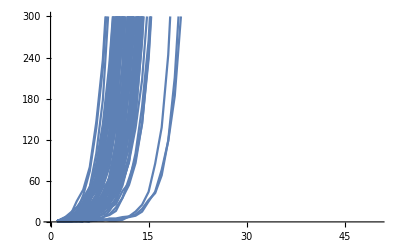

```mathematica
newN[b_, d_, gen_][i_]:=If[i==0,0,RandomInteger[PoissonDistribution[(1-d+b)i / (1- Flatten /@(1/(0!))D[Nest[poissonGF[b, d],z,gen],{z,0}]/.z->0)]]];
muhighSurv=Table[NestWhileList[newN[0.2, 0.1, 1],1,Positive,1,100],{100}];
Show[Table[ListLinePlot[muhighSurv⟦i⟧,PlotRange->{{0,50},{0,300}}],{i,100}]]
```

iv) 
if we plug in the values of b and d into μ=1 -d + b = 1 - 0.1 + 0.2 = 1.1 we see that μ>1. After 1 generation we see that probability of one individual leaving a range of k =0 is 0.3,  k=1 offspring is slightly higher at 0.37, k=2 is 0.2 and decreases further for up to k=10 calculated here. Here, we are using the moment generation function for Poisson distribution beacuse we assume that offspring distribution follows Poisson.

{{0,0.332871},{1,0.366158},{2,0.201387},{3,0.0738419},{4,0.0203065},{5,0.00446744},{6,0.00081903},{7,0.000128705},{8,0.0000176969},{9,2.16295×10^-6},{10,2.37925×10^-7}}

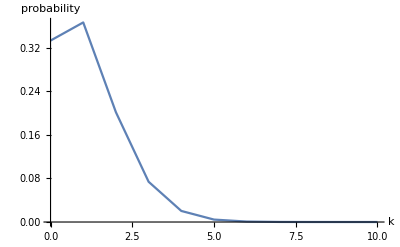

```mathematica
poissonGF[b_, d_][z_]:=Exp[-(1-d+b)(1-z)];
gen1 =1;
pd1=Table[{k,1/(k!)D[Nest[poissonGF[0.2, 0.1],z,gen1],{z,k}]/.z->0},{k,0,10}];
pd1
ListLinePlot[pd1,PlotRange-> All, AxesLabel->{"k","probability"}]
```

v)
Here I use the same code as above and just set the number of generations to 5. We see that after 5 generations leaving k=0 offspring is quite high at 0.66, k=1 is low at 0.06 and so on for k up to k=10

{{0,0.657874},{1,0.0591849},{2,0.057335},{3,0.0484259},{4,0.0392993},{5,0.0313303},{6,0.0246698},{7,0.019247},{8,0.0149111},{9,0.0114868},{10,0.00880683}}

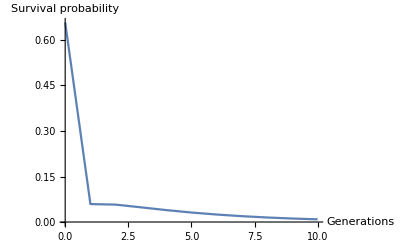

```mathematica
gen2 = 5;
pd5=Table[{k,1/(k!)D[Nest[poissonGF[0.2, 0.1],z,gen2],{z,k}]/.z->0},{k,0,10}];
pd5
ListLinePlot[pd5,PlotRange-> All, AxesLabel->{"Generations","Survival probability"}]
```